```mathematica
SetDirectory[NotebookDirectory[]];
```

## Model waiting times as from a negative binomial process for counts http://stats.stackexchange.com/questions/37814/poisson-is-to-exponential-as-gamma-poisson-is-to-what

```mathematica
PDF[ParetoDistribution[β,α,0],t]//TraditionalForm//Magnify
```

Piecewise[{{(α ((β+t)/β)^(-α-1))/β, t≥0}, {0, True}}]

### Generate waiting times from this process

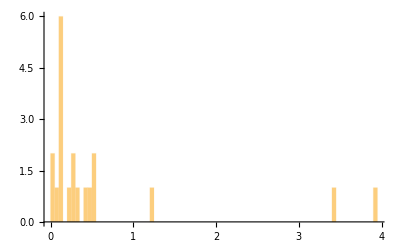

```mathematica
nSample = 20;
data=RandomVariate[ParetoDistribution[1,3,0],{nSample}];
Histogram[data,100]
```

### Fit the exponential distribution to these values

```mathematica
PDF[ExponentialDistribution[λ],t]//TraditionalForm//Magnify
```

Piecewise[{{λ ⅇ^(λ (-t)), t≥0}, {0, True}}]

### Algebraically derive an estimate of the mean number of visits per hour

```mathematica
Solve[D[Simplify[Likelihood[ExponentialDistribution[λ],{t1,t2,t3}],{t1>0,t2>0,t3>0}],λ]==0,λ][[2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{λ→3/(t1+t2+t3)}

```mathematica
lambdaEst =FindMaximum[{LogLikelihood[ExponentialDistribution[λ],data],λ>0},λ][[2,1,2]]
```

1.95113

### Graph the log likelihood near your estimated value. What does this show?

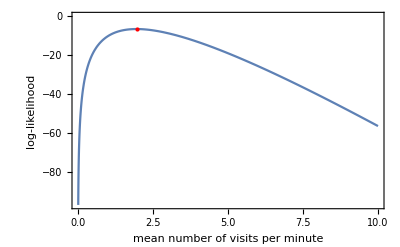

```mathematica
Plot[LogLikelihood[ExponentialDistribution[λ],data],{λ,0,10},Epilog->{Red,PointSize[Large],Point[{lambdaEst,FindMaximum[{LogLikelihood[ExponentialDistribution[λ],data],λ>0},λ][[1]]}]},Frame->{True,True,False,False},FrameLabel->{"mean number of visits per minute", "log-likelihood"},BaseStyle->{FontSize->Medium}]
```

### Estimate confidence intervals around your parameter

#### Information matrix

```mathematica
asympVar=(-(D[LogLikelihood[ExponentialDistribution[λ],data],{λ,2}]/.{λ->lambdaEst})^-1)/nSample;
asympStd  = Sqrt[asympVar];
```

```mathematica
{lambdaEst - 1.96*asympVar,lambdaEst + 1.96*asympVar}
```

{1.93248,1.96979}

### What is the probability that you will wait?

#### 1 minutes

```mathematica
CDF[ExponentialDistribution[lambdaEst],1]
```

0.857887

#### 5 minutes

```mathematica
CDF[ExponentialDistribution[lambdaEst],5]
```

0.999942

#### Half an hour

```mathematica
CDF[ExponentialDistribution[lambdaEst],30]
```

1.

## Evaluate your model

### Generating fake data from the MLE, we see an inability of the model to generate the extremes we see in the sample. c.f. the above where we calculated the probability of waiting 5 minutes or more

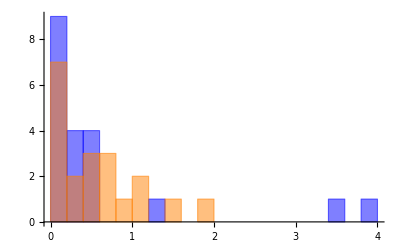

```mathematica
fakeData = RandomVariate[ExponentialDistribution[lambdaEst],{nSample}];
Histogram[{data,fakeData},20,ChartStyle->{Blue,Orange}]
```

## Using the correct model - a Pareto distribution type II

### Estimate the parameters of your new model

```mathematica
EstimatedDistribution[data,ParetoDistribution[β,α,0]]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {β} = {4292.77}. Try perturbing the initial point(s).

ParetoDistribution[4292.77,8383.85,0]

```mathematica
{betaEst,alphaEst}=Module[{lTemp=FindMaximum[{LogLikelihood[ParetoDistribution[β,α,0],data],β>0,α>0},{{β,1},{α,1}}][[2]]},{lTemp[[1,2]],lTemp[[2,2]]}]
```

{0.445928,1.63459}

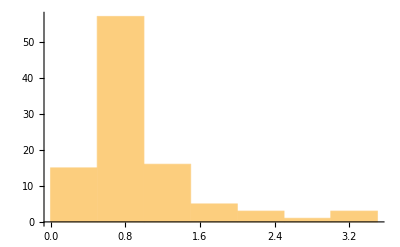

```mathematica
Histogram@RandomVariate[ParetoDistribution[betaEst,alphaEst],{100}]
```

### Use your new model to estimate the probability that you will wait

#### 1 minutes

```mathematica
CDF[ParetoDistribution[betaEst,alphaEst,0],1]
```

0.85381

#### 5 minutes

```mathematica
CDF[ParetoDistribution[betaEst,alphaEst,0],5]
```

0.983269

#### Half an hour

```mathematica
CDF[ParetoDistribution[betaEst,alphaEst,0],30]
```

0.998996